```mathematica
Clear[boat,mass,com,submerged,submass,water,cob,arm]
boatFunc[n_?NumberQ,d_?NumberQ,xVal_]:=boatFunc[n,d,xVal]=Exp[Abs[y/(n*(xVal^2-4))]]+(xVal^2-4)/6≤z≤d
boat:= boat=ImplicitRegion[boatFunc[.4,1,x],{x,y,z}]
mass :=mass= 250*N[RegionMeasure[boat]]
com:=com=N[RegionCentroid[boat]]
submerged[d_,t_]:=ImplicitRegion[2*(Abs[y/2]^2+Abs[x/5]^4)<z<2&&If[t<90,z<N[Tan[t Degree]]*y+d,z>N[Tan[t Degree]]*y+d],{{x,-5,5},{y,-2,2},{z,0,2}}]
submass[d_,t_]:=1000*N[RegionMeasure[submerged[d,t]]]
water[t_]:=water[t]=FindRoot[submass[d,t]==mass,{d,-20,20}]
cob[t_]:=cob[t]=N[RegionCentroid[submerged[d,t]/.water[t]]]
arm[t_?NumberQ]:=Cross[cob[t]-com,{0,-Sin[t Degree],Cos[t Degree]}][[1]]
```

```mathematica
points = Map[arm,Range[0,180,20]]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2 (1/625 Abs[«1»]^4+1/4 Abs[«1»]^2)<z<2&&z<0.+d&&-5≤x≤5&&-2≤y≤2&&0≤z≤2,{x,y,z}].

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2. (0.0016 Abs[«1»]^4+0.25 Abs[«1»]^2)<z<2.&&z<0.+d&&-5.≤x≤5.&&-2.≤y≤2.&&0.≤z≤2.,{x,y,z}].

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2 (1/625 Abs[«1»]^4+1/4 Abs[«1»]^2)<z<2&&z<d+0.36397 y&&-5≤x≤5&&-2≤y≤2&&0≤z≤2,{x,y,z}].

General::stop: Further output of RegionMeasure::nmet will be suppressed during this calculation.

{0.,0.118057,0.405587,1.44344,1.35439,0.76315,0.055926,-0.659214,-1.27682,1.70177×10^-18}

```mathematica
angles = Range[0,180,20]
newPoints = Transpose[{angles,points}]
```

{0,20,40,60,80,100,120,140,160,180}

{{0,0.},{20,0.118057},{40,0.405587},{60,1.44344},{80,1.35439},{100,0.76315},{120,0.055926},{140,-0.659214},{160,-1.27682},{180,1.70177×10^-18}}

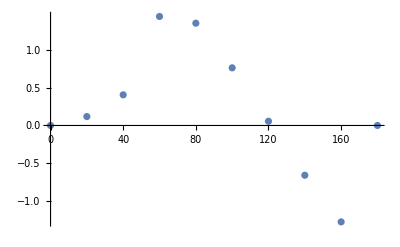

```mathematica
ListPlot[newPoints]
```

```mathematica
Tan[π]//AbsoluteTiming
```

{3.64673×10^-6,0}

```mathematica
mass
```

230.95

```mathematica
mass//AbsoluteTiming
```

{2.73361,230.95}

```mathematica
mass//AbsoluteTiming
```

{0.368731,9988.79}

```mathematica
RegionMeasure[boat]//AbsoluteTiming
```

{0.370875,(640 EllipticK[-1])/21}

```mathematica
N[RegionMeasure[boat]]//AbsoluteTiming
```

{0.369039,39.9552}

```mathematica
boatFunc[n_?NumberQ,d_?NumberQ,xVal_]:=Exp[Abs[y/(n*(xVal^2-4))]]+(xVal^2-4)/6≤z≤d
```

```mathematica
ImplicitRegion[boatFunc[.4,1,x],{x,y,z}]
```

ImplicitRegion[ⅇ^(2.5 Abs[y/(-4+x^2)])+1/6 (-4+x^2)≤z≤1,{x,y,z}]

```mathematica
RegionBounds[ImplicitRegion[boatFunc[.4,1,x],{x,y,z}]]
```

{{-1.99954,1.99966},{-0.817324,0.817321},{0.333333,1.}}